```mathematica
d=ConstantArray[0,128];
p = RandomSample[Range[128],64];
d[[p]] =1;
```

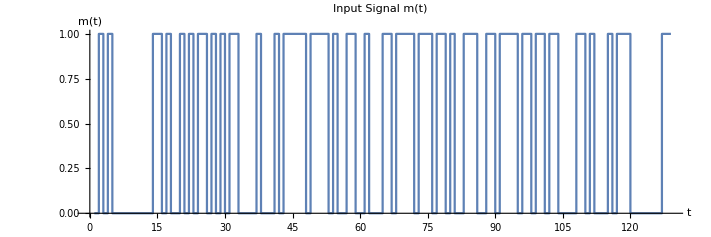

```mathematica
ListStepPlot[d, 
PlotLabel->"Input Signal m(t)",
AxesLabel->{t,m[t]},
AspectRatio->1/3]
```

```mathematica
qpsk={};
```

```mathematica
For[i=1,i<129,i+=2,
If[d[[i;;i+1]]=={0,0},AppendTo[qpsk,1+ⅉ],
If[d[[i;;i+1]]=={0,1},AppendTo[qpsk,-1+ⅉ],
If[d[[i;;i+1]]=={1,0},AppendTo[qpsk,-1-ⅉ],AppendTo[qpsk,1-ⅉ]]
]
]
]
```

```mathematica
qpsk
```

{-1+ⅈ,-1+ⅈ,1+ⅈ,1+ⅈ,1+ⅈ,1+ⅈ,-1+ⅈ,-1-ⅈ,-1-ⅈ,-1+ⅈ,-1+ⅈ,-1+ⅈ,-1-ⅈ,-1-ⅈ,-1-ⅈ,1-ⅈ,1+ⅈ,1+ⅈ,-1-ⅈ,1+ⅈ,-1-ⅈ,1-ⅈ,1-ⅈ,-1-ⅈ,1-ⅈ,1-ⅈ,-1+ⅈ,1+ⅈ,1-ⅈ,1+ⅈ,-1-ⅈ,1+ⅈ,1-ⅈ,-1+ⅈ,1-ⅈ,-1-ⅈ,1-ⅈ,-1-ⅈ,1-ⅈ,-1+ⅈ,1+ⅈ,1-ⅈ,-1-ⅈ,-1+ⅈ,-1-ⅈ,1-ⅈ,1-ⅈ,-1+ⅈ,-1-ⅈ,1-ⅈ,-1+ⅈ,-1-ⅈ,1+ⅈ,-1+ⅈ,-1-ⅈ,-1-ⅈ,1+ⅈ,-1-ⅈ,1-ⅈ,-1-ⅈ,1+ⅈ,1+ⅈ,1+ⅈ,1-ⅈ}

```mathematica
s[t_]:=Sum[qpsk[[k]]*Exp[(ⅈ*2*Pi*k*t)/64],{k,1,64}]/8;
```

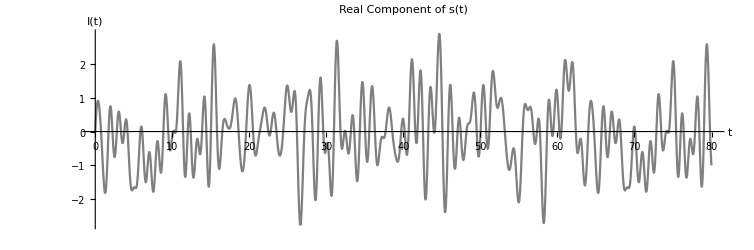

```mathematica
Plot[Re[s[t]],{t,0,80},
PlotLabel->"Real Component of s(t)",
AxesLabel->{t,"I(t)"},
PlotStyle->Gray,
AspectRatio->1/3]
```

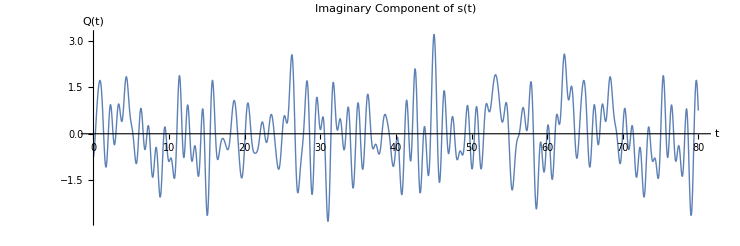

```mathematica
Plot[Im[s[t]],{t,0,80},
PlotLabel->"Imaginary Component of s(t)",
AxesLabel->{t,Q[t]},
PlotStyle->Thick,
AspectRatio->1/3]
```

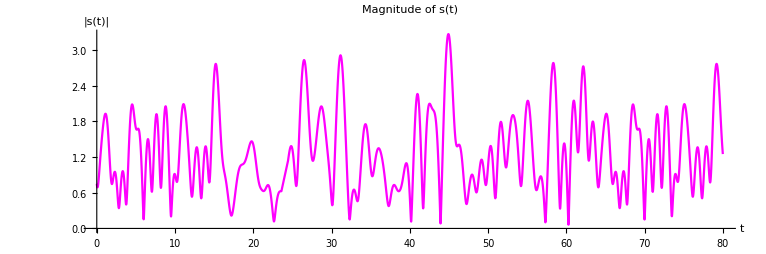

```mathematica
Plot[Abs[s[t]],{t,0,80},
PlotLabel->"Magnitude of s(t)",
AxesLabel->{t,"|s(t)|"},
PlotStyle->Magenta,
AspectRatio->1/3]
```

```mathematica
arg = {};
For[i=0.1,i<81,i+=0.1,
AppendTo[arg,{i,Arg[s[i]]}]]
```

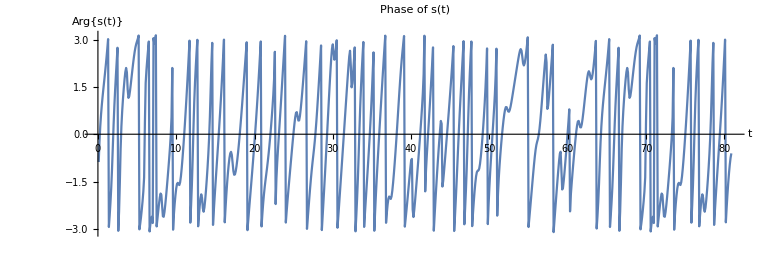

```mathematica
ListLinePlot[arg,
AspectRatio->1/3,
PlotLabel->"Phase of s(t)",
AxesLabel->{t,"Arg{s(t)}"}]
```

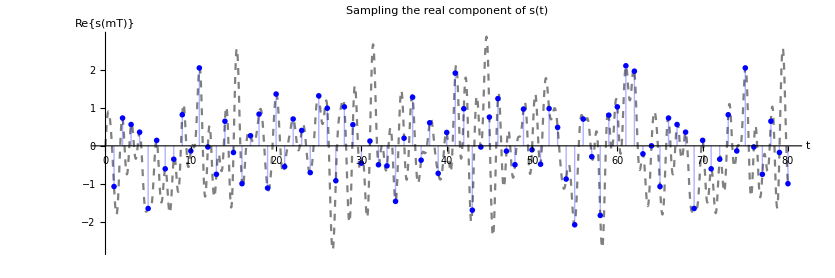

```mathematica
Show[
Plot[Re[s[t]],{t,0,80},
PlotStyle->{Gray,Dashed},
AspectRatio->1/3,
PlotLabel->"Sampling the real component of s(t)",
AxesLabel->{t,"Re{s(mT)}"}],
ListPlot[Table[Re[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Small}]]
```

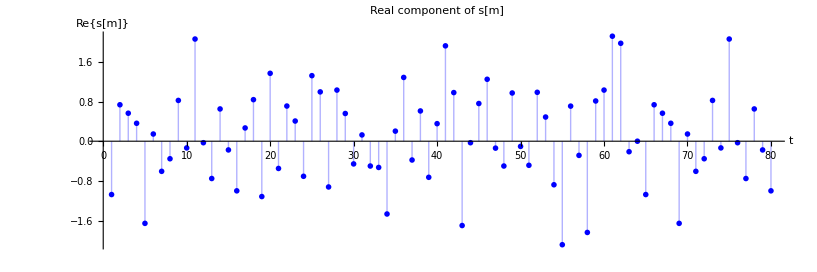

```mathematica
ListPlot[Table[Re[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium},
PlotLabel->"Real component of s[m]",
AxesLabel->{t,"Re{s[m]}"}]
```

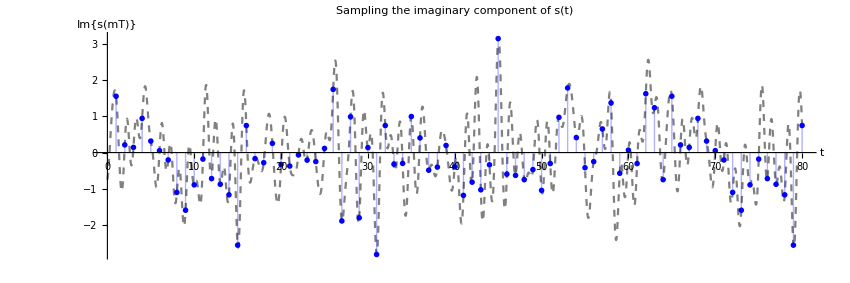

```mathematica
Show[
Plot[Im[s[t]],{t,0,80},
 PlotStyle->{Gray,Dashed},
AspectRatio->1/3,
PlotLabel->"Sampling the imaginary component of s(t)",
AxesLabel->{t,"Im{s(mT)}"}],
ListPlot[Table[Im[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium}]]
```

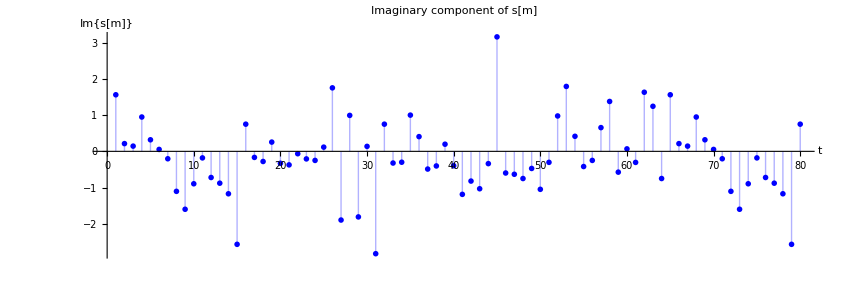

```mathematica
ListPlot[Table[Im[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium},
PlotLabel->"Imaginary component of s[m]",
AxesLabel->{t,"Im{s[m]}"}]
```

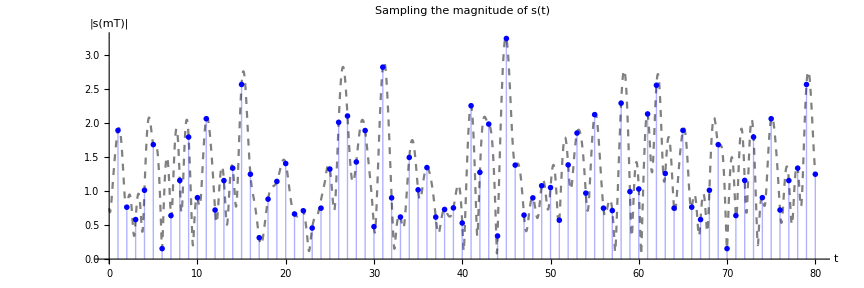

```mathematica
Show[
Plot[Abs[s[t]],{t,0,80},
PlotStyle->{Gray,Dashed},
AspectRatio->1/3,
PlotLabel->"Sampling the magnitude of s(t)",
AxesLabel->{t,"|s(mT)|"}],
ListPlot[Table[Abs[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium}]]
```

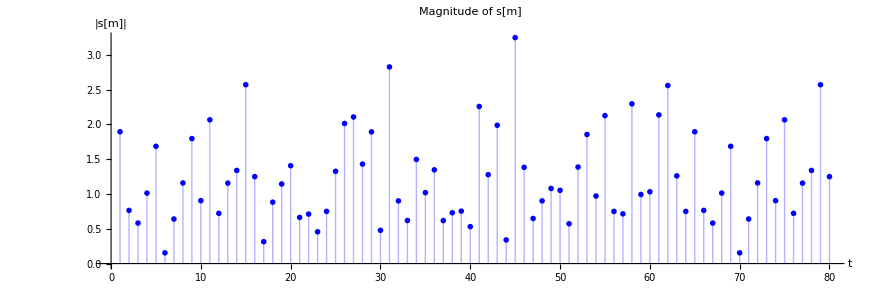

```mathematica
ListPlot[Table[Abs[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium},
PlotLabel->"Magnitude of s[m]",
AxesLabel->{t,"|s[m]|"}]
```

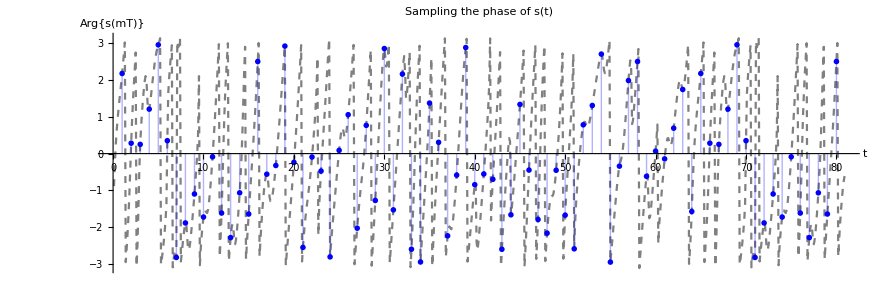

```mathematica
Show[
ListLinePlot[arg,
PlotStyle->{Gray,Dashed},
AspectRatio->1/3,
PlotLabel->"Sampling the phase of s(t)",
AxesLabel->{t,"Arg{s(mT)}"}],
ListPlot[Table[Arg[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium}]]
```

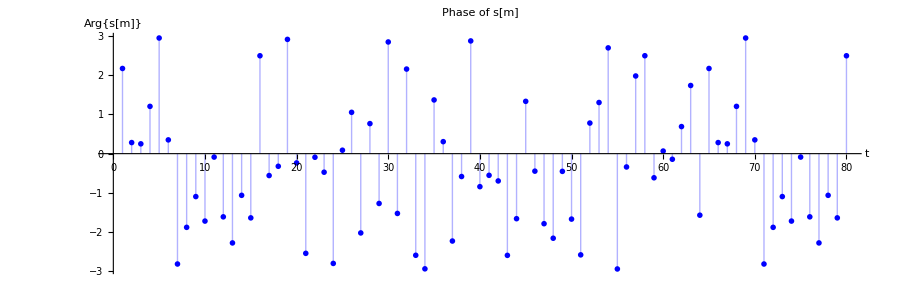

```mathematica
ListPlot[Table[Arg[s[i]],{i,1,80,1}],
PlotStyle->Blue,
Filling->Axis,
AspectRatio->1/3,
PlotMarkers->{Automatic,Medium},
PlotLabel->"Phase of s[m]",
AxesLabel->{t,"Arg{s[m]}"}]
```

```mathematica
ImT = Table[Re[s[i]],{i,1,64,1}];
QmT = Table[Im[s[i]],{i,1,64,1}];
```

```mathematica
sm = ImT + ⅈ QmT;
```

```mathematica
x[l_]:=Sum[sm[[m]]*Exp[(-ⅈ*2*Pi*l*m)/64],{m,1,64}]/8
```

```mathematica
recovered ={};
For[i=1,i<65,i++,
If[N[x[i]]==1+1ⅈ,recovered=Join[recovered,{0,0}],
If[N[x[i]]==-1+1ⅈ,recovered=Join[recovered,{0,1}],
If[N[x[i]]==-1-1ⅈ,recovered=Join[recovered,{1,0}],recovered=Join[recovered,{1,1}]]
]
]
]
```

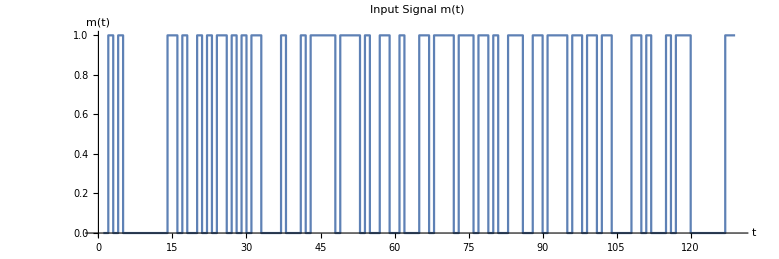

```mathematica
ListStepPlot[recovered, 
PlotLabel->"Input Signal m(t)",
AxesLabel->{t,m[t]},
AspectRatio->1/3]
```

```mathematica
recovered
```

{0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,1,1,0,1,0,0,1,1,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,1,1,0,1,1,0,1,0,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,1,1}

```mathematica
d
```

{0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,1,1,0,1,0,0,1,1,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,1,1,0,1,1,0,1,0,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,1,1}